```mathematica
(* Load the individual notes *)
Fs=44100;
files=FileNames[NotebookDirectory[]<>"C4*.wav"];
files=Append[files,"~/Dropbox/UofR/Research/Piano/060.3 Piano.ff.C4.aiff"];
testList=Import[#,"Data"]&/@files;
notes = {};
(* Cut the initial silence *)
NTHR = 0.01;
For[i=1, i <= Dimensions[testList][[1]], i++,
note = testList[[i,1]];
note = If[Dimensions[note][[1]]==2,(note[[1]]+note[[2]])/2.0,note];
start = First[FirstPosition[Abs[note],_?(#>NTHR&)]];
notes = Append[notes,note[[start;;]]]]
(* Align the notes through cross-correlation in the time domain on the first 10000 samples *)
lags={};
CORRLEN=2000;
For[i=1, i≤Length[notes], i++,
corr=ListCorrelate[notes[[1]][[1;;CORRLEN]],notes[[i]][[1;;CORRLEN]],1];
lag = First[FirstPosition[corr,Max[corr]]]-1;
lags = Append[lags,If[lag≤CORRLEN/2, lag, lag-CORRLEN]]]
alignedNotes={notes[[1]]};
For[i=2,i≤Length[notes],i++,
note=If[lags[[i]]≥0,notes[[i]][[1+lags[[i]];;]],Join[ConstantArray[0,-lags[[i]]],notes[[i]]]];
alignedNotes=Append[alignedNotes,note]]
(* alignedNotes is an array of waveforms *)

(* Helper functions *)
WrapPhase[phi_]:=FractionalPart[phi/(2*Pi)]*2*Pi-Pi

Unwrap[args_]:=Module[{pairs,diffs,j,len=Length[args],corr=0},pairs=Partition[args,2,1];
diffs=Map[#[[1]]-#[[2]]&,pairs];
PrependTo[diffs,0];
diffs=2*Pi*Sign[Chop[diffs,Pi]];
Table[corr+=diffs[[j]];
corr+args[[j]],{j,1,len}]]

PickPeaks[v_]:=Select[Range[2,Length[v]-1],(v[[#-1]]<v[[#]] && v[[#+1]]<v[[#]])&]
```

```mathematica
Manipulate[ListLinePlot[{alignedNotes[[1]][[start;;start+length]], alignedNotes[[note]][[start;;start+length]]},PlotRange->All],{note,2,Length[alignedNotes],1},{start,1,200000,1},{{length, 10000},100,100000,1}]
```

```mathematica
NFFT = 2048;
HOP = 1024;
NROW = NFFT/2+1;
S=Chop[Transpose[SpectrogramArray[notes[[1]],NFFT,HOP, HammingWindow]]];
```

```mathematica
Image[Reverse[Abs[S[[1;;NROW,;;]]]]]
```

```mathematica
Image[Reverse[Arg[S[[1;;NROW,;;]]]]]
```

```mathematica
binSum=Total[Abs[S[[1;;NROW,;;]]],{2}];
peaks=PickPeaks[binSum]
```

{7,13,19,25,29,33,37,45,50,54,56,58,62,66,70,74,82,86,91,95,99,104,107,111,116,119,124,129,132,137,142,144,149,155,159,162,166,172,176,184,189,197,202,209,216,220,222,224,230,234,238,240,243,248,250,254,258,262,264,269,272,276,278,281,286,290,293,295,298,301,305,309,312,316,321,323,325,328,331,336,342,346,350,353,357,362,366,369,374,378,382,385,388,394,399,404,406,411,413,415,417,421,424,427,431,434,438,441,444,451,455,458,461,464,470,473,476,479,482,487,490,492,495,497,500,503,505,509,515,518,523,525,529,531,534,536,539,543,545,548,552,555,560,567,572,577,580,582,585,588,591,595,600,604,610,613,617,621,626,630,633,640,644,646,649,653,655,658,662,669,671,673,676,678,681,686,688,691,694,697,703,706,709,712,716,721,724,727,730,733,735,737,740,742,744,746,749,751,756,762,766,772,778,782,785,788,791,793,797,801,803,808,813,816,819,824,828,833,836,841,843,845,849,851,854,857,862,865,868,871,875,878,881,887,892,895,898,905,910,914,919,924,926,929,933,938,940,943,946,950,953,959,961,963,965,967,969,972,976,980,984,986,990,992,994,997,999,1003,1005,1008,1011,1014,1018,1024}

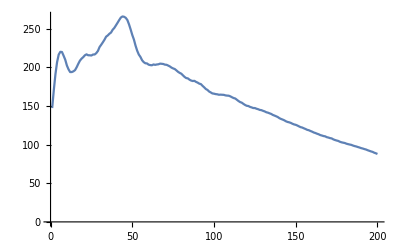

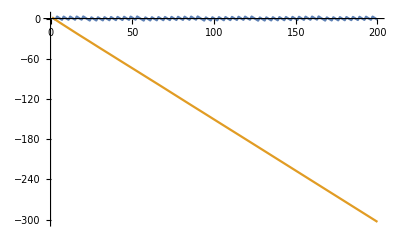

```mathematica
bin = 13;
frames = 200;
ListLinePlot[Abs[S[[bin,1;;frames]]],PlotRange->All]
ListLinePlot[{Arg[S[[bin,1;;frames]]],Unwrap[Arg[S[[bin,1;;frames]]]]},PlotRange->All]
```